# Graph Learning

## Synthetic Data

We will make a Barabasi-Albert graph to define signals on.

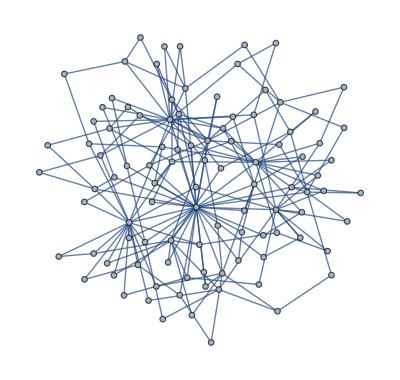

```mathematica
nVertices = 100;
k = 2;
degreeDist := BarabasiAlbertGraphDistribution[nVertices, k];
G = RandomGraph[degreeDist]
```

The goal of our project is to distinguish graph signals generated by two separate processes. To test the neural net, we can generate a bunch of graphs from two different processes, and compare them!

```mathematica
processA[G_] :=Module[
{x = Table[0, {i, G // VertexCount}],r},
Do[Do[Do[
If[EdgeQ[G, i <-> j] && EdgeQ[G, j <-> k] && EdgeQ[G, k <-> i],
If[Random[] ≤ 3/4, 
r = RandomVariate[ExponentialDistribution[1]],
r = 0];
x[[i]] += r;
x[[j]] += r;
x[[k]] += r],
{k, 1, j}], {j, 1, i}], {i, 1, G // VertexCount}];
x];
```

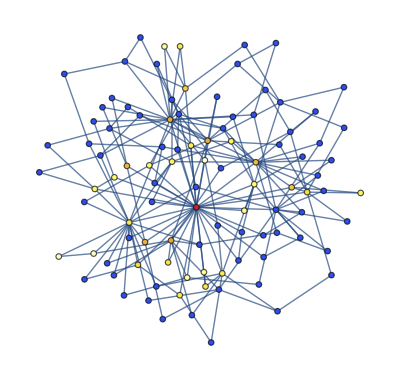

```mathematica
x = processA[G];
ColorFN = ColorData["TemperatureMap"];
colors = Table[v -> ColorFN[(x[[v]]/Max[x])^(1/8)], {v, G // VertexCount}];
Graph[G, VertexStyle -> colors]
```

```mathematica
processB[G_] := Table[
RandomVariate[ExponentialDistribution[1/(VertexDegree[G][[i]])]],
{i, G // VertexCount}];
```

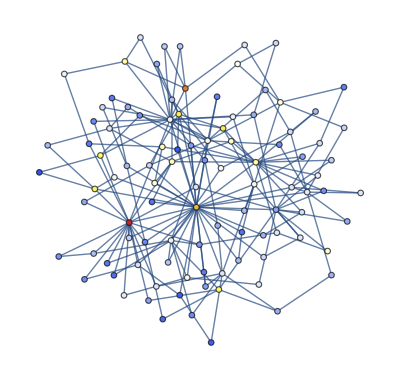

```mathematica
x = processB[G];
ColorFN = ColorData["TemperatureMap"];
colors = Table[v -> ColorFN[(x[[v]]/Max[x])^(1/2)], {v, G // VertexCount}];
Graph[G, VertexStyle -> colors]
```

## More Shennanigans

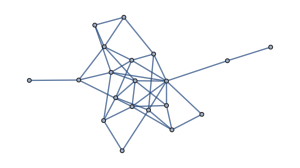

```mathematica
G = RandomGraph[{20, 40}]
```

```mathematica
LaplacianMatrix[G_] := DiagonalMatrix[VertexDegree[G]]- AdjacencyMatrix[G];
```

```mathematica
SpectralPartition[G_]:= Module[
{L = LaplacianMatrix[G], v},
v = Eigenvectors[L][[-2]] // N;
# > 0& /@ v];
```

```mathematica
GraphBisect[G_, minSize_] := Module[{p, v1, v2, G1, G2},
If[Length[VertexList[G]] ≤ minSize,
{G},
p = SpectralPartition[G];
v1 = VertexList[G][[Position[p, True] // Flatten]];
v2 = VertexList[G][[Position[p, False] // Flatten]];
G1 = Subgraph[G, v1];
G2 = Subgraph[G, v2];
GraphBisect[G1, minSize]~Join~GraphBisect[G2, minSize]
]];
```

```mathematica
GraphPartition[G_, minSize_] := Module[
{subgraphs = GraphBisect[G, minSize],subgraphEnum},
subgraphEnum = Table[i, {i, Length[subgraphs]}];
Table[
Select[subgraphEnum, VertexQ[subgraphs[[#]], v]&],
{v, G // VertexList // Length}] // Flatten];
```

```mathematica
p = GraphPartition[G, 4];
```

```mathematica
p
```

{2,3,2,3,3,4,5,1,6,2,4,4,2,6,4,6,5,1,3,1}

```mathematica
colors = {Red, Green, Blue, Orange, Black, Yellow};
style = Table[v -> colors[[p[[v]]]], {v, VertexCount[G]}];
```

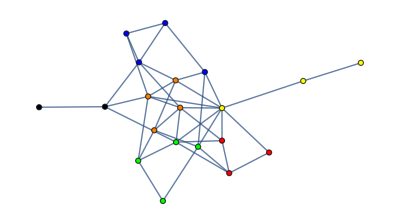

```mathematica
Graph[G, VertexStyle -> style]
```

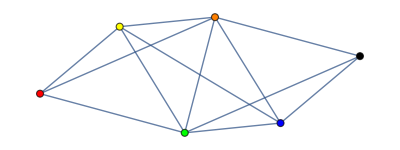

```mathematica
SimpleGraph[p[[# // First]]<-> p[[# // Last]]& /@ EdgeList[G], 
VertexStyle -> Table[v -> colors[[v]], {v, 6}]]
```

```mathematica
x= 1
```

1

```mathematica
x += 1
```

2